# Data preprocessing: SMD data set NANOG and GATA6

## Supplementary material for Fischer et al "The salt-and-pepper pattern in mouse blastocysts is compatible with signalling beyond the nearest neighbours."

## Initialisation

```mathematica
baseDirectory=StringReplace[ParentDirectory[NotebookDirectory[]],"dataPreprocessing"->"analysisCode"];
```

```mathematica
<<(FileNameJoin[{baseDirectory,"CellNucleiSegmentation_v8.m"}]) (*code from Schmitz et al. Scientific Reports 2017*)
```

```mathematica
<<(FileNameJoin[{baseDirectory,"neighbourAnaFunctions_v2.m"}])(*code from Fischer et al. PLOS One 2020 and extensions*)
```

```mathematica
shiftValue[expName_,val_,threshold_,experiments_]:=Switch[expName,experiments[[1,1]],val+(threshold[[1]]-threshold[[1]]),experiments[[2,1]],val+(threshold[[1]]-threshold[[2]]),experiments[[3,1]],val+(threshold[[1]]-threshold[[3]]),experiments[[4,1]],val+(threshold[[1]]-threshold[[4]])]
```

```mathematica
zCorrection[fileName_,slope_,channels_:{"Dapi","Nanog","Gata6","Gata4"}]:=Block[{nucleiFeatures,nucleiFeaturesWithCorr,exportFName},
nucleiFeatures="NucleiFeatures"/.Import[fileName];
nucleiFeaturesWithCorr=Join[#,
Table[channels[[i]]<>"-AvgLnCorr"->Log[channels[[i]]<>"-Avg"/.#]-slope[[i]]*("Centroid"/.#)[[3]],{i,1,Length[channels]}]&@#]&/@nucleiFeatures;
exportFName=StringReplace[fileName,"Features.mx"->"Features_ZCorrected.mx"];
Export[exportFName,"NucleiFeatures"->nucleiFeaturesWithCorr]
]
```

```mathematica
fontOption="Arial";
```

```mathematica
<<ErrorBarPlots`
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
plotMeanStdLighter[xValues_,yValues_,smooth_,xLabel_,yLabel_,colour_]:=
Show[Table[ListLinePlot[{Transpose[{xValues[[i]],MeanFilter[#[[All,1]]+#[[All,2]],smooth]}],
Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]}&@yValues[[i]],PlotRange->{0,All},
PlotStyle->{Directive[Opacity[0.5],Lighter[colour[i],0.7]],Directive[Opacity[0.5],Lighter[colour[i],0.7]]},Filling->1->{2},FillingStyle->Directive[Opacity[0.5],Lighter[colour[i],0.5]],Frame->{True,True,None,None},FrameStyle->Directive[Black,(*Thick,*)FontFamily->fontOption,14],(*TicksStyle->Thick,*)FrameLabel->{xLabel,yLabel}],{i,1,Length[xValues]}],
ListLinePlot[Table[Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]],{i,1,Length[xValues]}],
PlotRange->{0,All},PlotStyle->Transpose[{ConstantArray[Thickness[0.007],Length[xValues]],Table[colour[i],{i,1,Length[xValues]}]}],Frame->{True,True,None,None},FrameStyle->Directive[Black,FontFamily->fontOption,14],FrameLabel->{xLabel,yLabel}]]
```

```mathematica
smoothedValues[unsmoothedData_,smooth_]:=Block[{xValues,yValues,lowerLimit,mean},
xValues=#[[All,1]]&/@unsmoothedData;
yValues=#[[All,2;;3]]&/@unsmoothedData;
Table[lowerLimit=Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]&@yValues[[i]];mean=Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]];Table[Join[mean[[i]],{(mean-lowerLimit)[[i,-1]]}],{i,1,Length[mean]}],{i,1,Length[xValues]}]
]
```

```mathematica
colourNegPos[i_]:={Lighter[Gray,0.3],Darker[Gray,0.7]}[[i]]
```

```mathematica
colour3[i_]:=Join[{Darker[Gray]},(ColorData[16]/@{3,6,4})][[i]]
```

```mathematica
colour2[i_]:={Darker[Gray],Darker[Purple],Darker[Green,0.7]}[[i]]
```

```mathematica
colour1[i_]:={Darker[Gray],Darker[Purple],Darker[Green,0.7],Darker[Cyan,0.5]}[[i]]
```

```mathematica
populationsColours={Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]};
```

## Converting data from MINS

renaming channels, tissue classification and rescaling of centroid position to µm

```mathematica
fNames=FileNames["*",FileNameJoin[{NotebookDirectory[],"DataFromMINS"}]];
```

```mathematica
convertFromMINS[#,StringReplace[StringDelete[#,".csv"]<>"_Features.mx","DataFromMINS"->"EmbryoFeatures"],"XinMicrons"->0.312,"YinMicrons"->0.312,"ZinMicrons"->1.0,"ImagingChannels"->{"CH1-Avg"->"Dapi-Avg","CH1-Sum"->"Dapi-Sum","CH2-Avg"->"Nanog-Avg","CH2-Sum"->"Nanog-Sum","CH3-Avg"->"Gata6-Avg","CH3-Sum"->"Gata6-Sum","CH4-Avg"->"Gata4-Avg","CH4-Sum"->"Gata4-Sum"},"NumberMeasurements"->16]&/@fNames;
```

## z-Correction

Use TE cells to determine curve for correction, do natural logarithm and linear fit (motivated by Saiz et al 2016) per experiment, per channel

#### 26

```mathematica
featuresFNames=FileNames["26*Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
nucleiFeatures[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Nanog-Avg,Nanog-Sum,Gata6-Avg,Gata6-Sum,Gata4-Avg,Gata4-Sum}

```mathematica
zAndExprPerEmbryo=Table[{#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@({"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","TE/ICM"}/.nucleiFeatures[[i]]),{i,1,Length[nucleiFeatures]}];
```

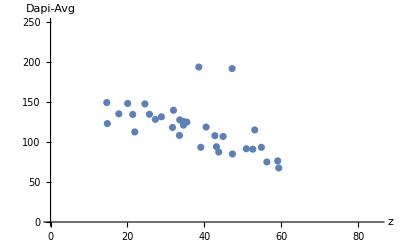
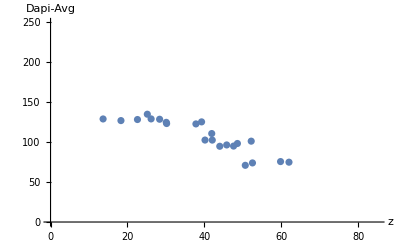
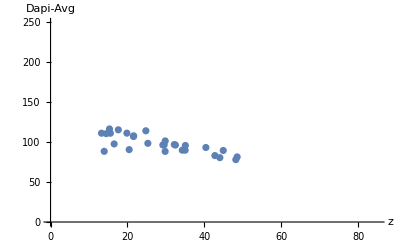
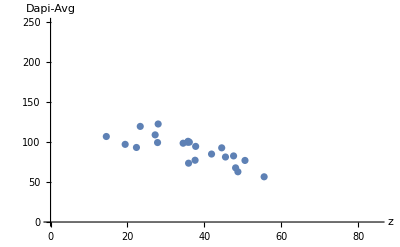
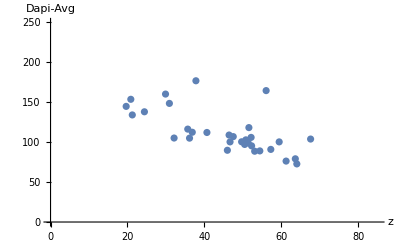
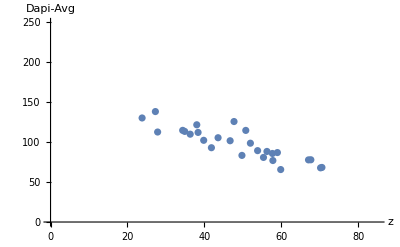
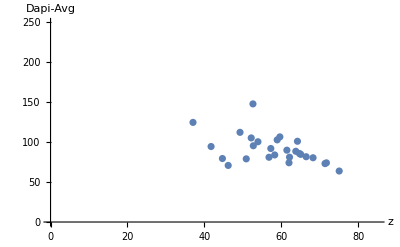
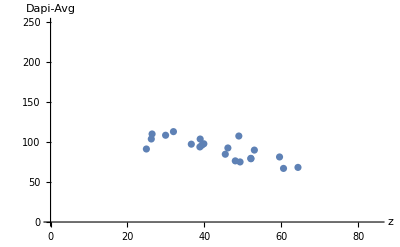

```mathematica
Table[ListPlot[Select[zAndExprPerEmbryo[[i]],#[[-1]]≠"TE"&][[All,{1,2}]],PlotRange->{{0,85},{0,250}},AxesLabel->{"z","Dapi-Avg"}],{i,1,Length[zAndExprPerEmbryo]}]
```

```mathematica
zAndExpr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]}&/@Flatten[{"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg","TE/ICM"}/.nucleiFeatures,1];
```

```mathematica
zAndExprTE=Select[zAndExpr,#[[-1]]=="TE"&];
```

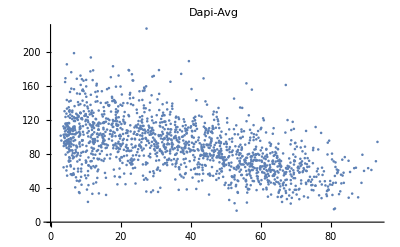
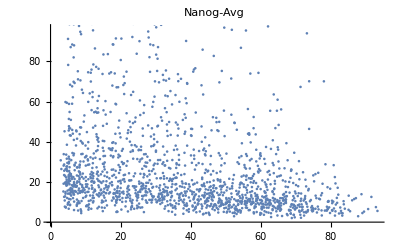
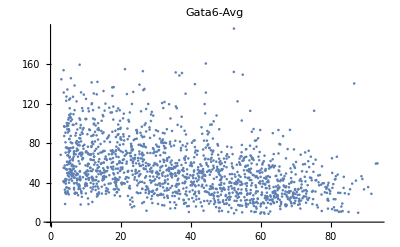
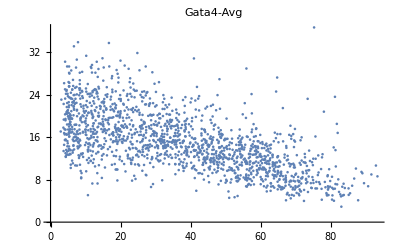

```mathematica
Table[ListPlot[zAndExprTE[[All,{1,i}]],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

```mathematica
lmLn26=Table[LinearModelFit[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],x,x],{i,{2,3,4,5}}]
```

{FittedModel[4.75216-0.00882867 x],FittedModel[3.49456-0.0143201 x],FittedModel[4.24231-0.0104759 x],FittedModel[3.08638-0.0114713 x]}

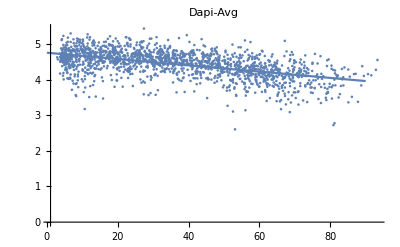
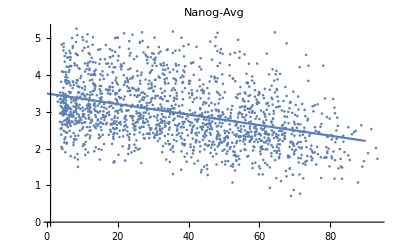
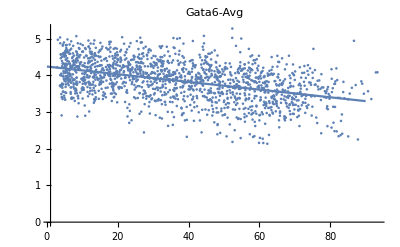
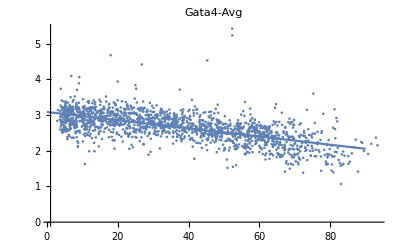

```mathematica
Table[Show[ListPlot[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],PlotRange->All],Plot[lmLn26[[i-1]][x],{x,0,90}],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

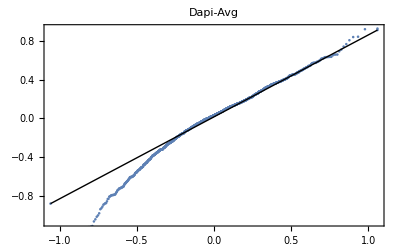
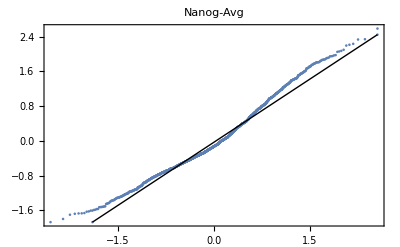
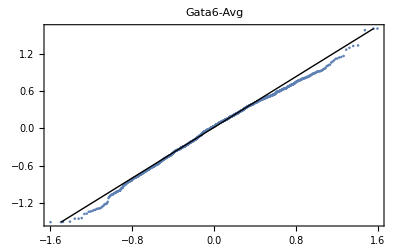
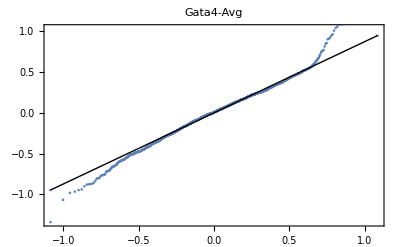

```mathematica
Table[QuantilePlot[lmLn26[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

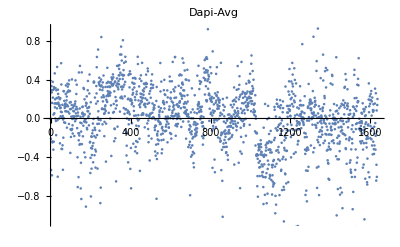
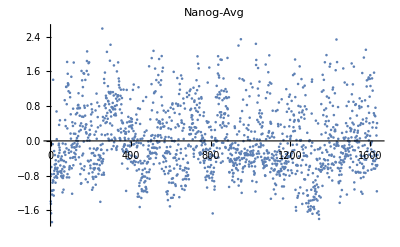
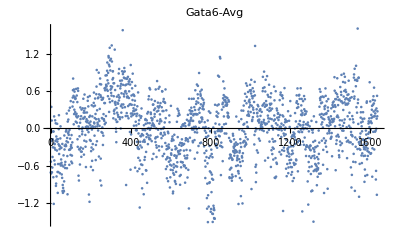
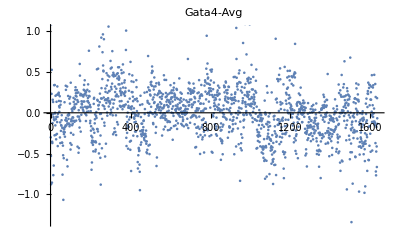

```mathematica
Table[ListPlot[lmLn26[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

```mathematica
slope26=Table[lmLn26[[i]]["BestFitParameters"][[2]],{i,1,Length[lmLn26]}]
```

{-0.00882867,-0.0143201,-0.0104759,-0.0114713}

corrected values

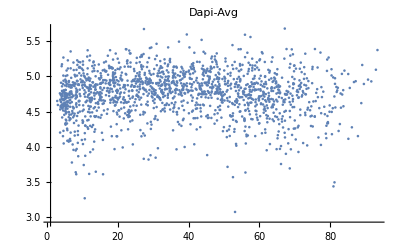
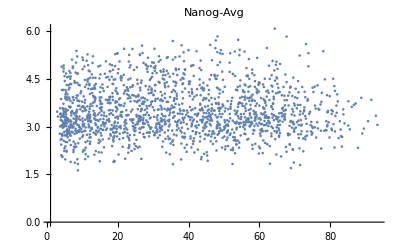
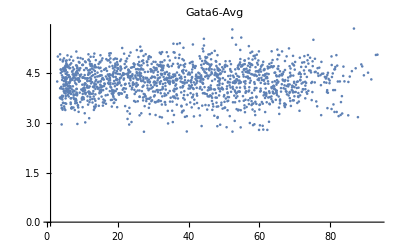
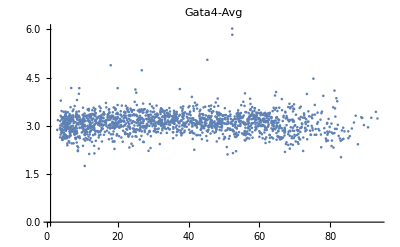

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slope26[[i-1]]*#[[1]]})&/@zAndExprTE[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

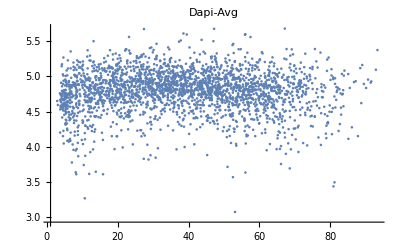
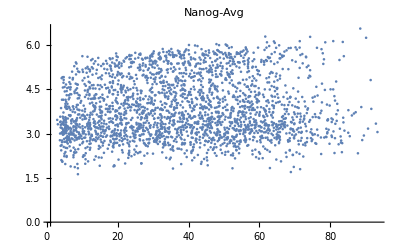
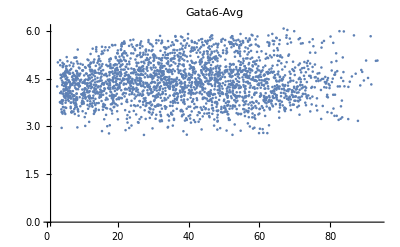
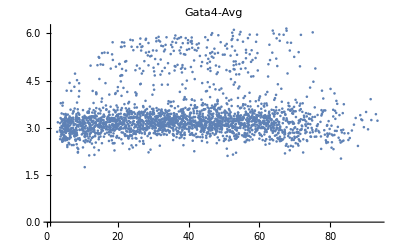

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slope26[[i-1]]*#[[1]]})&/@zAndExpr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

Export corrected values for 26

```mathematica
zCorrection[#,slope26]&/@featuresFNames;
```

Test

```mathematica
corrFeaturesFNames=FileNames["26*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeaturesZCorr=("NucleiFeatures"/.Import[#])&/@corrFeaturesFNames;
```

```mathematica
nucleiFeaturesZCorr[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Nanog-Avg,Nanog-Sum,Gata6-Avg,Gata6-Sum,Gata4-Avg,Gata4-Sum,Dapi-AvgLnCorr,Nanog-AvgLnCorr,Gata6-AvgLnCorr,Gata4-AvgLnCorr}

```mathematica
zAndExprZCorr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr","TE/ICM"}/.nucleiFeaturesZCorr,1];
```

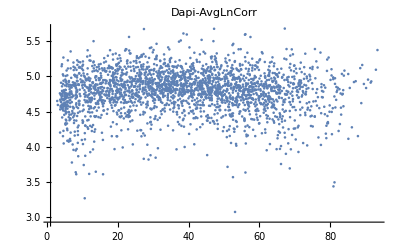
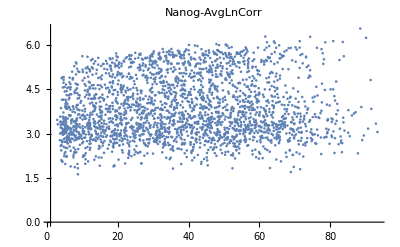
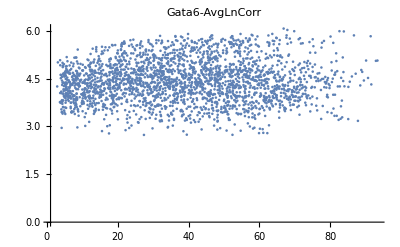
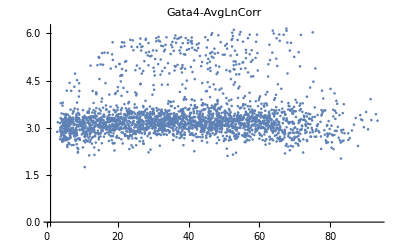

```mathematica
Table[ListPlot[zAndExprZCorr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr"}[[i-1]]],{i,{2,3,4,5}}]
```

#### 27

```mathematica
featuresFNames=FileNames["27*Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
nucleiFeatures[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Nanog-Avg,Nanog-Sum,Gata6-Avg,Gata6-Sum,Gata4-Avg,Gata4-Sum}

```mathematica
zAndExprPerEmbryo=Table[{#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@({"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","TE/ICM"}/.nucleiFeatures[[i]]),{i,1,Length[nucleiFeatures]}];
```

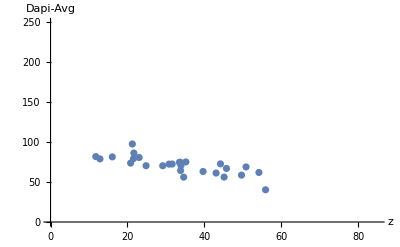
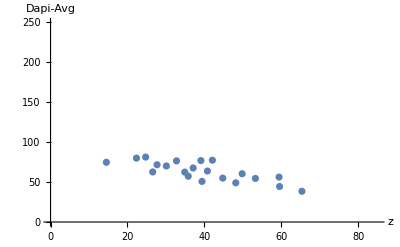
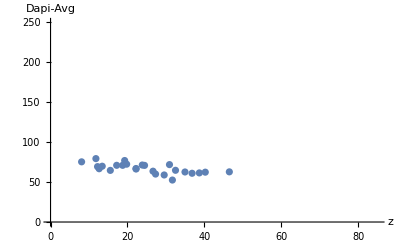
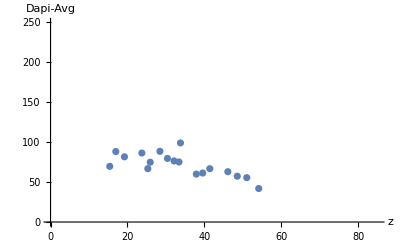
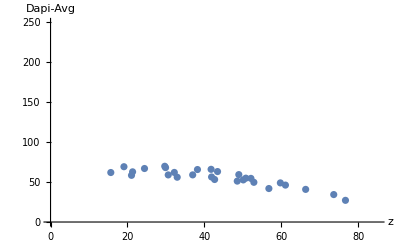
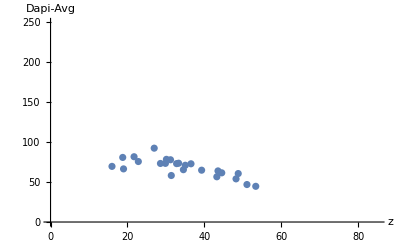
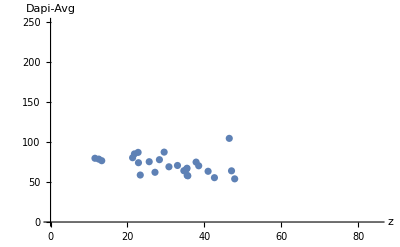
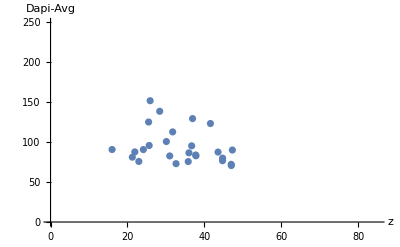

```mathematica
Table[ListPlot[Select[zAndExprPerEmbryo[[i]],#[[-1]]≠"TE"&][[All,{1,2}]],PlotRange->{{0,85},{0,250}},AxesLabel->{"z","Dapi-Avg"}],{i,1,Length[zAndExprPerEmbryo]}]
```

```mathematica
zAndExpr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]}&/@Flatten[{"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg","TE/ICM"}/.nucleiFeatures,1];
```

```mathematica
zAndExprTE=Select[zAndExpr,#[[-1]]=="TE"&];
```

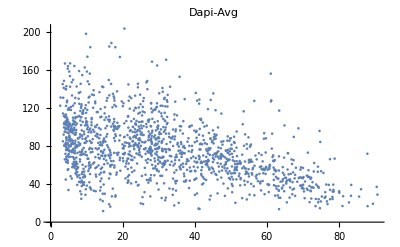
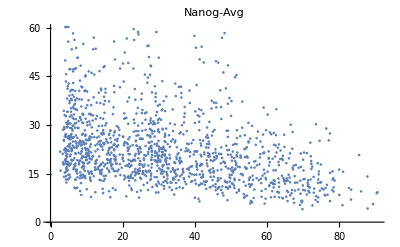
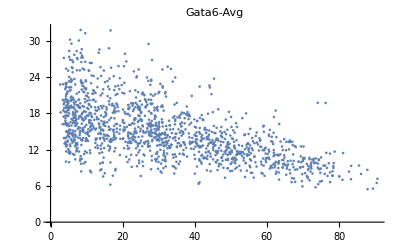
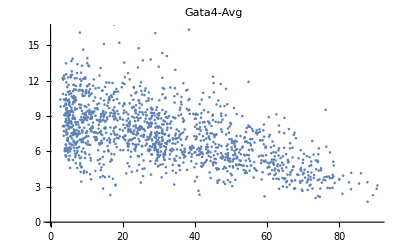

```mathematica
Table[ListPlot[zAndExprTE[[All,{1,i}]],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

```mathematica
lmLn27=Table[LinearModelFit[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],x,x],{i,{2,3,4,5}}]
```

{FittedModel[4.57574-0.0103687 x],FittedModel[3.35803-0.0104185 x],FittedModel[2.95556-0.00933118 x],FittedModel[2.26031-0.00990249 x]}

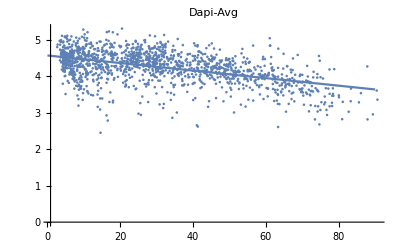
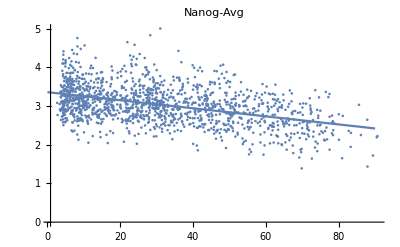
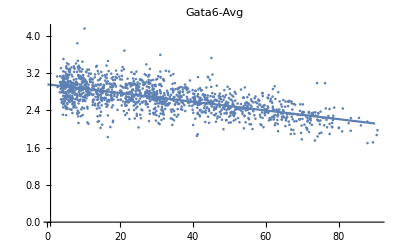
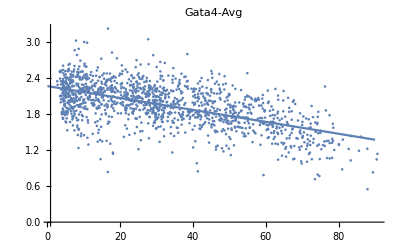

```mathematica
Table[Show[ListPlot[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],PlotRange->All],Plot[lmLn27[[i-1]][x],{x,0,90}],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

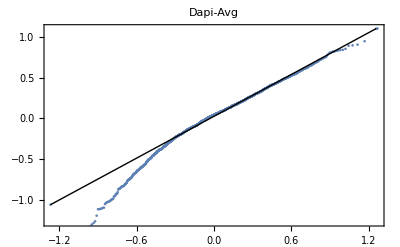
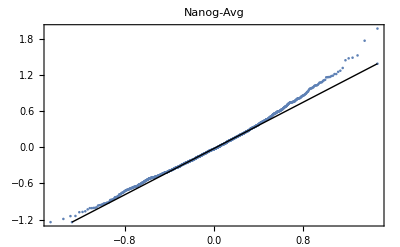
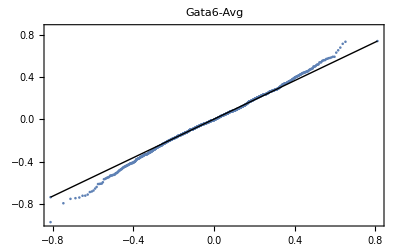
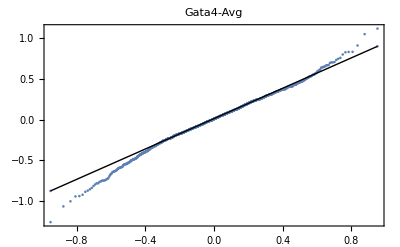

```mathematica
Table[QuantilePlot[lmLn27[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

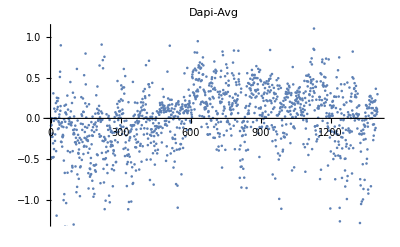
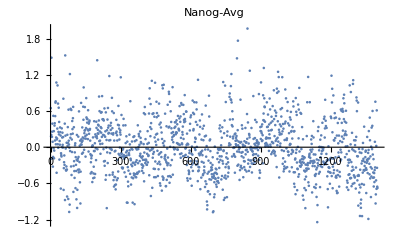
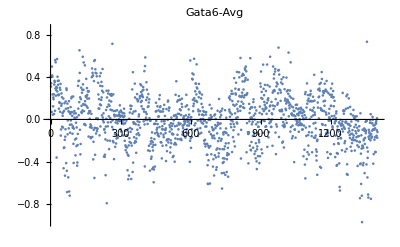
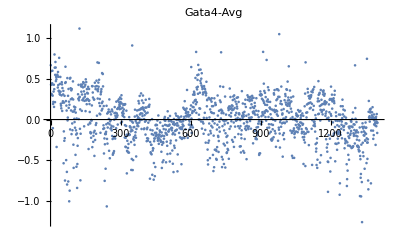

```mathematica
Table[ListPlot[lmLn27[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

```mathematica
slope27=Table[lmLn27[[i]]["BestFitParameters"][[2]],{i,1,Length[lmLn27]}]
```

{-0.0103687,-0.0104185,-0.00933118,-0.00990249}

corrected values

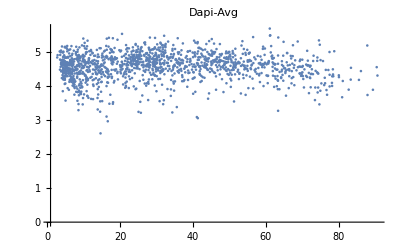
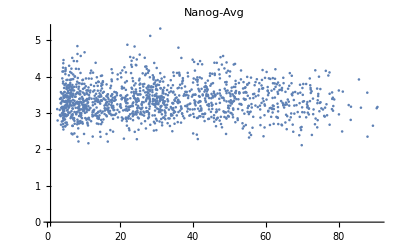
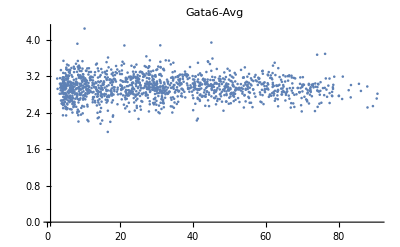
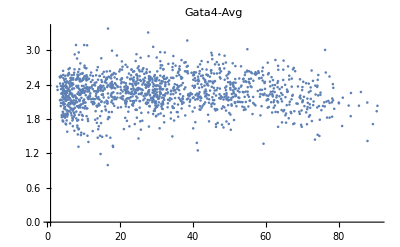

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slope27[[i-1]]*#[[1]]})&/@zAndExprTE[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

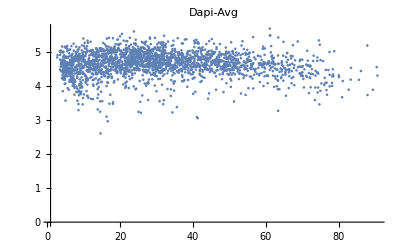
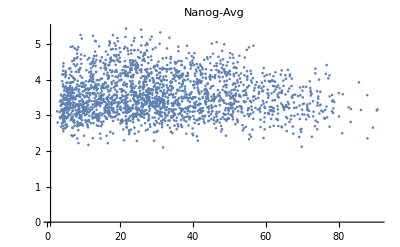
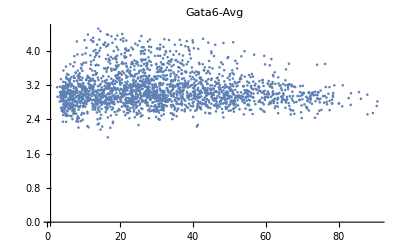
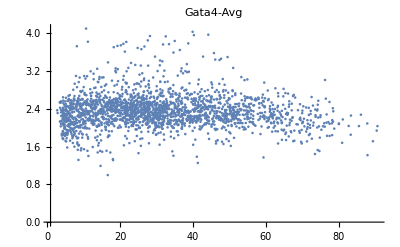

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slope27[[i-1]]*#[[1]]})&/@zAndExpr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

Export corrected values for 27

```mathematica
zCorrection[#,slope27]&/@featuresFNames;
```

Test

```mathematica
corrFeaturesFNames=FileNames["27*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeaturesZCorr=("NucleiFeatures"/.Import[#])&/@corrFeaturesFNames;
```

```mathematica
nucleiFeaturesZCorr[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Nanog-Avg,Nanog-Sum,Gata6-Avg,Gata6-Sum,Gata4-Avg,Gata4-Sum,Dapi-AvgLnCorr,Nanog-AvgLnCorr,Gata6-AvgLnCorr,Gata4-AvgLnCorr}

```mathematica
zAndExprZCorr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr","TE/ICM"}/.nucleiFeaturesZCorr,1];
```

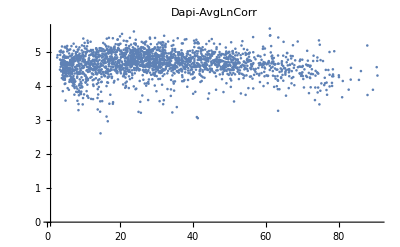
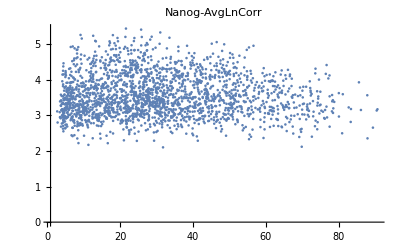
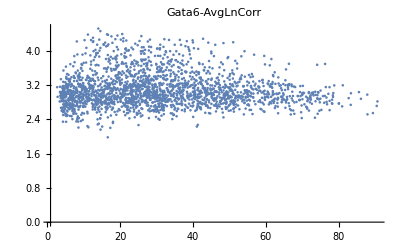
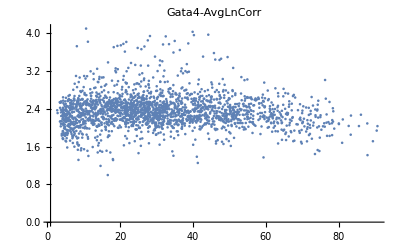

```mathematica
Table[ListPlot[zAndExprZCorr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr"}[[i-1]]],{i,{2,3,4,5}}]
```

#### 28

```mathematica
featuresFNames=FileNames["28*Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
nucleiFeatures[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Nanog-Avg,Nanog-Sum,Gata6-Avg,Gata6-Sum,Gata4-Avg,Gata4-Sum}

```mathematica
zAndExprPerEmbryo=Table[{#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@({"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","TE/ICM"}/.nucleiFeatures[[i]]),{i,1,Length[nucleiFeatures]}];
```

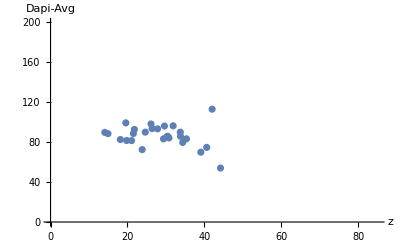
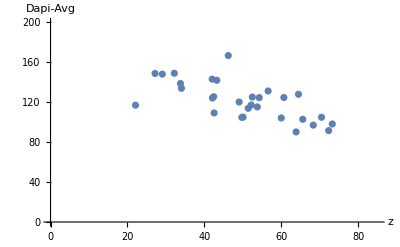
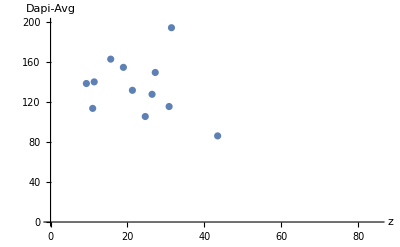
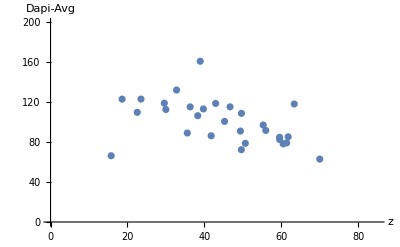
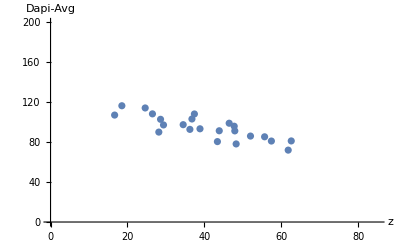
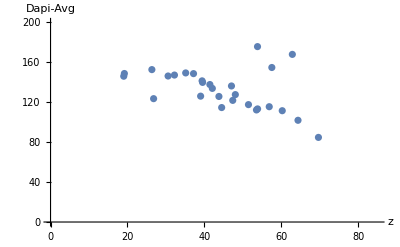
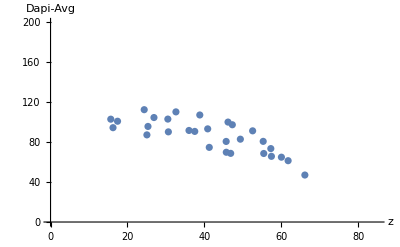
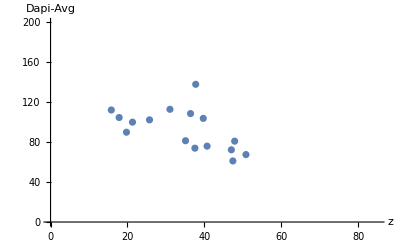
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[Select[zAndExprPerEmbryo[[i]],#[[-1]]≠"TE"&][[All,{1,2}]],PlotRange->{{0,85},{0,200}},AxesLabel->{"z","Dapi-Avg"}],{i,1,Length[zAndExprPerEmbryo]}]
```

```mathematica
zAndExpr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]}&/@Flatten[{"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg","TE/ICM"}/.nucleiFeatures,1];
```

```mathematica
zAndExprTE=Select[zAndExpr,#[[-1]]=="TE"&];
```

```mathematica
Table[ListPlot[zAndExprTE[[All,{1,i}]],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lmLn28=Table[LinearModelFit[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],x,x],{i,{2,3,4,5}}]
```

{FittedModel[4.6161-0.00777347 x],FittedModel[2.469-0.00920458 x],FittedModel[2.97679-0.00962979 x],FittedModel[2.22603-0.0107801 x]}

```mathematica
Table[Show[ListPlot[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],PlotRange->All],Plot[lmLn28[[i-1]][x],{x,0,90}],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[QuantilePlot[lmLn28[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[lmLn28[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
slope28=Table[lmLn28[[i]]["BestFitParameters"][[2]],{i,1,Length[lmLn28]}]
```

{-0.00777347,-0.00920458,-0.00962979,-0.0107801}

corrected values

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slope28[[i-1]]*#[[1]]})&/@zAndExprTE[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slope28[[i-1]]*#[[1]]})&/@zAndExpr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Export corrected values for 28

```mathematica
zCorrection[#,slope28]&/@featuresFNames;
```

Test

```mathematica
corrFeaturesFNames=FileNames["28*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeaturesZCorr=("NucleiFeatures"/.Import[#])&/@corrFeaturesFNames;
```

```mathematica
nucleiFeaturesZCorr[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Nanog-Avg,Nanog-Sum,Gata6-Avg,Gata6-Sum,Gata4-Avg,Gata4-Sum,Dapi-AvgLnCorr,Nanog-AvgLnCorr,Gata6-AvgLnCorr,Gata4-AvgLnCorr}

```mathematica
zAndExprZCorr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr","TE/ICM"}/.nucleiFeaturesZCorr,1];
```

```mathematica
Table[ListPlot[zAndExprZCorr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr"}[[i-1]]],{i,{2,3,4,5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### 1504

```mathematica
featuresFNames=FileNames["1504*Features.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
nucleiFeatures
```

{{{Inlier/Outlier→1,EmbryoId→1,CellID→1,Size→990.962,TE/ICM→TE,Centroid→{123.605,71.37,7.2765},Dapi-Avg→73.457,Dapi-Sum→748000.,Nanog-Avg→22.612,Nanog-Sum→230000.,Gata6-Avg→58.062,Gata6-Sum→591000.,Gata4-Avg→2.6631,Gata4-Sum→27110},62,{Inlier/Outlier→1,EmbryoId→1,CellID→64,Size→68.1408,TE/ICM→TE,Centroid→{27.4058,114.866,65.067},Dapi-Avg→7.5229,Dapi-Sum→5266,Nanog-Avg→6.7129,Nanog-Sum→4699,Gata6-Avg→7.4014,Gata6-Sum→5181,Gata4-Avg→2.1943,Gata4-Sum→1536}},30}
 |  |  |  |

```mathematica
nucleiFeatures[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Nanog-Avg,Nanog-Sum,Gata6-Avg,Gata6-Sum,Gata4-Avg,Gata4-Sum}

```mathematica
zAndExprPerEmbryo=Table[{#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]]}&/@({"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","TE/ICM"}/.nucleiFeatures[[i]]),{i,1,Length[nucleiFeatures]}];
```

```mathematica
Table[ListPlot[Select[zAndExprPerEmbryo[[i]],#[[-1]]≠"TE"&][[All,{1,2}]],PlotRange->{{0,85},{0,150}},AxesLabel->{"z","Dapi-Avg"}],{i,1,Length[zAndExprPerEmbryo]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
zAndExpr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]}&/@Flatten[{"Centroid","Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg","TE/ICM"}/.nucleiFeatures,1];
```

```mathematica
zAndExprTE=Select[zAndExpr,#[[-1]]=="TE"&];
```

```mathematica
Table[ListPlot[zAndExprTE[[All,{1,i}]],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lmLn1504=Table[LinearModelFit[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],x,x],{i,{2,3,4,5}}]
```

{FittedModel[4.44458-0.00655913 x],FittedModel[3.29268-0.00985373 x],FittedModel[3.955-0.0108348 x],FittedModel[1.02276-0.00976462 x]}

```mathematica
Table[Show[ListPlot[{#[[1]],Log[#[[2]]]}&/@zAndExprTE[[All,{1,i}]],PlotRange->All],Plot[lmLn1504[[i-1]][x],{x,0,90}],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[QuantilePlot[lmLn1504[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[lmLn1504[[i-1]]["FitResiduals"],PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
slope1504=Table[lmLn1504[[i]]["BestFitParameters"][[2]],{i,1,Length[lmLn1504]}]
```

{-0.00655913,-0.00985373,-0.0108348,-0.00976462}

corrected values

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slope1504[[i-1]]*#[[1]]})&/@zAndExprTE[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[({#[[1]],Log[#[[2]]]}-{0,slope1504[[i-1]]*#[[1]]})&/@zAndExpr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-Avg","Nanog-Avg","Gata6-Avg","Gata4-Avg"}[[i-1]]],{i,{2,3,4,5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Export corrected values for 1504

```mathematica
zCorrection[#,slope1504]&/@featuresFNames;
```

Test

```mathematica
corrFeaturesFNames=FileNames["1504*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeaturesZCorr=("NucleiFeatures"/.Import[#])&/@corrFeaturesFNames;
```

```mathematica
nucleiFeaturesZCorr[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Nanog-Avg,Nanog-Sum,Gata6-Avg,Gata6-Sum,Gata4-Avg,Gata4-Sum,Dapi-AvgLnCorr,Nanog-AvgLnCorr,Gata6-AvgLnCorr,Gata4-AvgLnCorr}

```mathematica
zAndExprZCorr={#[[1,3]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr","TE/ICM"}/.nucleiFeaturesZCorr,1];
```

```mathematica
Table[ListPlot[zAndExprZCorr[[All,{1,i}]],PlotRange->All,PlotLabel->{"Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr"}[[i-1]]],{i,{2,3,4,5}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Expression vs z position:

### 26

```mathematica
featuresFNames=FileNames["26*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
nucleiFeatures[[1,1]]//Keys
```

{Inlier/Outlier,EmbryoId,CellID,Size,TE/ICM,Centroid,Dapi-Avg,Dapi-Sum,Nanog-Avg,Nanog-Sum,Gata6-Avg,Gata6-Sum,Gata4-Avg,Gata4-Sum,Dapi-AvgLnCorr,Nanog-AvgLnCorr,Gata6-AvgLnCorr,Gata4-AvgLnCorr}

```mathematica
zAndExpr={#[[1,3]],Exp[#[[2]]],Exp[#[[3]]],Exp[#[[4]]],Exp[#[[5]]],Exp[#[[6]]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr","TE/ICM"}/.nucleiFeatures,1];
```

```mathematica
{zMin,zMax,numCells}=Through[{Min,Max,Length}[zAndExpr[[All,1;;2]][[All,1]]]]
```

{2.9096,93.336,2495}

```mathematica
avgDapiAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,2}]],{-10,200,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgNanogAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,200,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata6AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,4}]],{-10,200,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata4AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,5}]],{-10,200,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
exprAlongZNanog26=Show[plotMeanStdLighter[{#[[All,1]]&@avgDapiAlongZ,#[[All,1]]&@avgNanogAlongZ,#[[All,1]]&@avgGata6AlongZ,#[[All,1]]&@avgGata4AlongZ},{#[[All,2;;3]]&@avgDapiAlongZ,#[[All,2;;3]]&@avgNanogAlongZ,#[[All,2;;3]]&@avgGata6AlongZ,#[[All,2;;3]]&@avgGata4AlongZ},0,"z position (µm)","Average per cell nucleus (a.u.)\n(mean ± std err., a.u.)",colour1],ImageSize->500,PlotRange->{0,All}]
```

-Graphics-

Why are they going up at the end?

```mathematica
SortBy[Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&][[-1]],#[[1]]&]
```

{{90.129,519.684},{90.677,23.8474},{91.417,123.834},{91.601,46.6007},{92.895,28.2493},{93.336,21.2368}}

```mathematica
Select[Table[{i,Select[nucleiFeatures[[i]],("Centroid"/.#)[[3]]>90&]},{i,1,Length[nucleiFeatures]}],#[[2]]≠{}&]
```

{{31,{{Inlier/Outlier→1,EmbryoId→1,CellID→63,Size→1380.14,TE/ICM→TE,Centroid→{56.9712,74.7458,91.601},Dapi-Avg→61.504,Dapi-Sum→872000.,Nanog-Avg→12.552,Nanog-Sum→178000.,Gata6-Avg→28.678,Gata6-Sum→407000.,Gata4-Avg→8.9771,Gata4-Sum→127000.,Dapi-AvgLnCorr→4.92782,Nanog-AvgLnCorr→3.84162,Gata6-AvgLnCorr→4.31573,Gata4-AvgLnCorr→3.24546},{Inlier/Outlier→1,EmbryoId→1,CellID→64,Size→941.122,TE/ICM→TE,Centroid→{87.6689,92.561,92.895},Dapi-Avg→71.774,Dapi-Sum→694000.,Nanog-Avg→7.4693,Nanog-Sum→72213,Gata6-Avg→59.243,Gata6-Sum→573000.,Gata4-Avg→10.656,Gata4-Sum→103000.,Dapi-AvgLnCorr→5.09366,Nanog-AvgLnCorr→3.34107,Gata6-AvgLnCorr→5.0548,Gata4-AvgLnCorr→3.43175},{Inlier/Outlier→1,EmbryoId→1,CellID→65,Size→564.011,TE/ICM→ICM+Epi,Centroid→{69.2515,95.5812,90.129},Dapi-Avg→56.739,Dapi-Sum→329000.,Nanog-Avg→142.96,Nanog-Sum→828000.,Gata6-Avg→61.566,Gata6-Sum→357000.,Gata4-Avg→11.799,Gata4-Sum→68361,Dapi-AvgLnCorr→4.83418,Nanog-AvgLnCorr→6.25322,Gata6-AvgLnCorr→5.06429,Gata4-AvgLnCorr→3.50192},{Inlier/Outlier→1,EmbryoId→1,CellID→66,Size→827.035,TE/ICM→ICM+Epi,Centroid→{65.0239,84.0902,91.417},Dapi-Avg→60.564,Dapi-Sum→515000.,Nanog-Avg→33.443,Nanog-Sum→284000.,Gata6-Avg→129.98,Gata6-Sum→1.1×10^6,Gata4-Avg→17.475,Gata4-Sum→148000.,Dapi-AvgLnCorr→4.91079,Nanog-AvgLnCorr→4.81894,Gata6-AvgLnCorr→5.82505,Gata4-AvgLnCorr→3.90945},{Inlier/Outlier→1,EmbryoId→1,CellID→67,Size→711.974,TE/ICM→TE,Centroid→{87.2102,74.2092,93.336},Dapi-Avg→94.559,Dapi-Sum→692000.,Nanog-Avg→5.5798,Nanog-Sum→40811,Gata6-Avg→59.489,Gata6-Sum→435000.,Gata4-Avg→8.6217,Gata4-Sum→63059,Dapi-AvgLnCorr→5.37326,Nanog-AvgLnCorr→3.05573,Gata6-AvgLnCorr→5.06357,Gata4-AvgLnCorr→3.22497}}},{33,{{Inlier/Outlier→1,EmbryoId→1,CellID→78,Size→568.878,TE/ICM→TE,Centroid→{89.2694,91.4254,90.677},Dapi-Avg→63.598,Dapi-Sum→372000.,Nanog-Avg→6.5089,Nanog-Sum→38038,Gata6-Avg→35.466,Gata6-Sum→207000.,Gata4-Avg→6.7582,Gata4-Sum→39495,Dapi-AvgLnCorr→4.95314,Nanog-AvgLnCorr→3.17167,Gata6-AvgLnCorr→4.51849,Gata4-AvgLnCorr→2.95094}}}}

```mathematica
featuresFNames[[{31,33}]]
```

### 27

```mathematica
featuresFNames=FileNames["27*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
zAndExpr={#[[1,3]],Exp[#[[2]]],Exp[#[[3]]],Exp[#[[4]]],Exp[#[[5]]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr"}/.nucleiFeatures,1];
```

```mathematica
{zMin,zMax,numCells}=Through[{Min,Max,Length}[zAndExpr[[All,1;;2]][[All,1]]]]
```

{2.6814,90.652,2161}

```mathematica
avgDapiAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,2}]],{-10,200,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgNanogAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata6AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,4}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata4AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,5}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
exprAlongZNanog27=Show[plotMeanStdLighter[{#[[All,1]]&@avgDapiAlongZ,#[[All,1]]&@avgNanogAlongZ,#[[All,1]]&@avgGata6AlongZ,#[[All,1]]&@avgGata4AlongZ},{#[[All,2;;3]]&@avgDapiAlongZ,#[[All,2;;3]]&@avgNanogAlongZ,#[[All,2;;3]]&@avgGata6AlongZ,#[[All,2;;3]]&@avgGata4AlongZ},0,"z position (µm)","Average per cell nucleus (a.u.)\n(mean ± std err., a.u.)",colour1],ImageSize->500,PlotRange->{0,All}]
```

-Graphics-

Why are they going up at the end?

```mathematica
SortBy[Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&][[-1]],#[[1]]&]
```

{{90.443,22.9506},{90.652,23.7479}}

```mathematica
Select[Table[{i,Select[nucleiFeatures[[i]],("Centroid"/.#)[[3]]>90&]},{i,1,Length[nucleiFeatures]}],#[[2]]≠{}&]
```

{{2,{{Inlier/Outlier→1,EmbryoId→1,CellID→83,Size→754.027,TE/ICM→TE,Centroid→{71.3045,67.7508,90.443},Dapi-Avg→37.025,Dapi-Sum→287000.,Nanog-Avg→8.9447,Nanog-Sum→69286,Gata6-Avg→6.4805,Gata6-Sum→50198,Gata4-Avg→2.8342,Gata4-Sum→21954,Dapi-AvgLnCorr→4.54937,Nanog-AvgLnCorr→3.13334,Gata6-AvgLnCorr→2.71274,Gata4-AvgLnCorr→1.93737},{Inlier/Outlier→1,EmbryoId→1,CellID→84,Size→924.768,TE/ICM→TE,Centroid→{63.9101,80.2807,90.652},Dapi-Avg→28.886,Dapi-Sum→274000.,Nanog-Avg→9.2353,Nanog-Sum→87735,Gata6-Avg→7.1873,Gata6-Sum→68279,Gata4-Avg→3.1093,Gata4-Sum→29538,Dapi-AvgLnCorr→4.3033,Nanog-AvgLnCorr→3.16749,Gata6-AvgLnCorr→2.81821,Gata4-AvgLnCorr→2.03208}}}}

```mathematica
featuresFNames[[2]]
```

### 28

```mathematica
featuresFNames=FileNames["28*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
zAndExpr={#[[1,3]],Exp[#[[2]]],Exp[#[[3]]],Exp[#[[4]]],Exp[#[[5]]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr"}/.nucleiFeatures,1];
```

```mathematica
{zMin,zMax,numCells}=Through[{Min,Max,Length}[zAndExpr[[All,1;;2]][[All,1]]]]
```

{2.9452,78.444,1762}

```mathematica
avgDapiAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,2}]],{-10,200,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgNanogAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata6AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,4}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata4AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,5}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
exprAlongZNanog28=Show[plotMeanStdLighter[{#[[All,1]]&@avgDapiAlongZ,#[[All,1]]&@avgNanogAlongZ,#[[All,1]]&@avgGata6AlongZ,#[[All,1]]&@avgGata4AlongZ},{#[[All,2;;3]]&@avgDapiAlongZ,#[[All,2;;3]]&@avgNanogAlongZ,#[[All,2;;3]]&@avgGata6AlongZ,#[[All,2;;3]]&@avgGata4AlongZ},0,"z position (µm)","Average per cell nucleus (a.u.)\n(mean ± std err., a.u.)",colour1],ImageSize->500,PlotRange->{0,All}]
```

-Graphics-

```mathematica
SortBy[Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&][[-1]],#[[1]]&]
```

{{70.014,4.99113},{70.15,5.93998},{70.156,6.07955},{70.455,50.2826},{70.491,50.8867},{70.517,5.99185},{70.52,6.04139},{70.549,14.5538},{70.589,6.65805},{70.701,62.8573},{70.906,11.438},{71.022,7.29894},{71.037,9.46385},{71.511,2.86383},{71.594,19.2991},{71.904,7.42279},{71.935,6.83179},{72.034,7.58654},{72.313,19.9393},{72.327,8.50294},{72.334,19.9432},{72.464,5.79567},{72.656,5.23442},{72.675,10.8785},{72.829,20.5895},{73.252,19.0406},{73.352,23.7356},{73.536,14.7393},{73.717,21.3202},{74.029,6.97324},{74.37,9.18703},{74.434,4.46766},{74.636,16.7653},{74.723,44.2366},{74.728,17.0067},{75.286,21.2624},{75.568,9.4138},{75.676,8.5851},{75.891,6.19736},{76.141,12.6839},{76.881,54.9699},{76.973,15.5701},{77.094,8.20362},{77.127,10.6441},{77.203,34.9799},{77.936,11.4187},{78.051,11.608},{78.444,29.3768}}

```mathematica
Length[%]
```

48

### 1504

```mathematica
featuresFNames=FileNames["1504*Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@featuresFNames;
```

```mathematica
zAndExpr={#[[1,3]],Exp[#[[2]]],Exp[#[[3]]],Exp[#[[4]]],Exp[#[[5]]]}&/@Flatten[{"Centroid","Dapi-AvgLnCorr","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr"}/.nucleiFeatures,1];
```

```mathematica
{zMin,zMax,numCells}=Through[{Min,Max,Length}[zAndExpr[[All,1;;2]][[All,1]]]]
```

{2.5062,82.924,1976}

```mathematica
avgDapiAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,2}]],{-10,200,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgNanogAlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata6AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,4}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
avgGata4AlongZ={#[[1,1]],#[[1,2]],#[[2,2]]}&/@(Through[{Mean,If[Length[#]>1,StandardDeviation[#]/Sqrt[Length[#]],{0,0}]&}[#]]&/@Select[Flatten[BinLists[zAndExpr[[All,{1,5}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&]);
```

```mathematica
exprAlongZNanog1504=Show[plotMeanStdLighter[{#[[All,1]]&@avgDapiAlongZ,#[[All,1]]&@avgNanogAlongZ,#[[All,1]]&@avgGata6AlongZ,#[[All,1]]&@avgGata4AlongZ},{#[[All,2;;3]]&@avgDapiAlongZ,#[[All,2;;3]]&@avgNanogAlongZ,#[[All,2;;3]]&@avgGata6AlongZ,#[[All,2;;3]]&@avgGata4AlongZ},0,"z position (µm)","Average per cell nucleus (a.u.)\n(mean ± std err., a.u.)",colour1],ImageSize->500,PlotRange->{0,All}]
```

-Graphics-

Why are they going up at the end?

```mathematica
SortBy[Select[Flatten[BinLists[zAndExpr[[All,{1,3}]],{-10,100,10},{0,10^6,10^6}],1],Length[#]>0&][[-1]],#[[1]]&]
```

{{81.267,7.71932},{82.561,7.85605},{82.924,10.8627}}

```mathematica
Select[Table[{i,Select[nucleiFeatures[[i]],("Centroid"/.#)[[3]]>81&]},{i,1,Length[nucleiFeatures]}],#[[2]]≠{}&]
```

{{28,{{Inlier/Outlier→1,EmbryoId→1,CellID→80,Size→324.545,TE/ICM→TE,Centroid→{100.149,86.2337,81.267},Dapi-Avg→71.597,Dapi-Sum→239000.,Nanog-Avg→3.4658,Nanog-Sum→11555,Gata6-Avg→9.5471,Gata6-Sum→31830,Gata4-Avg→0.70516,Gata4-Sum→2351,Dapi-AvgLnCorr→4.80409,Nanog-AvgLnCorr→2.04373,Gata6-AvgLnCorr→3.13675,Gata4-AvgLnCorr→0.444211},{Inlier/Outlier→1,EmbryoId→1,CellID→81,Size→142.025,TE/ICM→TE,Centroid→{93.2942,87.1291,82.561},Dapi-Avg→78.735,Dapi-Sum→115000.,Nanog-Avg→3.4825,Nanog-Sum→5081,Gata6-Avg→9.6319,Gata6-Sum→14053,Gata4-Avg→0.68883,Gata4-Sum→1005,Dapi-AvgLnCorr→4.90762,Nanog-AvgLnCorr→2.06128,Gata6-AvgLnCorr→3.15961,Gata4-AvgLnCorr→0.433416},{Inlier/Outlier→1,EmbryoId→1,CellID→82,Size→71.3532,TE/ICM→TE,Centroid→{99.4094,79.6567,82.924},Dapi-Avg→96.064,Dapi-Sum→70415,Nanog-Avg→4.7981,Nanog-Sum→3517,Gata6-Avg→11.745,Gata6-Sum→8609,Gata4-Avg→0.78172,Gata4-Sum→573,Dapi-AvgLnCorr→5.10892,Nanog-AvgLnCorr→2.38533,Gata6-AvgLnCorr→3.36189,Gata4-AvgLnCorr→0.563463}}}}

```mathematica
featuresFNames[[28]]
```

## Rescaling because of squeezing when mounting the embryos

separating embryos in early/mid and late 
assume that early and mid blastocysts are spherical, calculate the main axes of these embryos and how much they deviate from spherical, for late embryos use the median rescaling factor

```mathematica
upperBoundCellNumber=91
```

91

```mathematica
rescale[fNamesAll_,upperBoundCellNumber_:upperBoundCellNumber]:=Block[{factorsForRescaling,nucleiFeatures,replace,res},
factorsForRescaling=Median[Cases[(nucleiFeatures="NucleiFeatures"/.Import[#];If[Length[nucleiFeatures]<upperBoundCellNumber,
(2*#[[2,1,2]])/#[[2,1,1]]&@Reap[rescaleCoordSphere["Centroid"/.nucleiFeatures]],
"no rescaling"
])&/@fNamesAll,_List]];
(nucleiFeatures="NucleiFeatures"/.Import[#];
If[Length[nucleiFeatures]<upperBoundCellNumber,
(replace="Centroid"->#&/@rescaleCoordSphere["Centroid"/.nucleiFeatures];
res="NucleiFeatures"->Table[ReplaceAll[nucleiFeatures[[i]],Rule["Centroid",{_,_,_}]->replace[[i]]],{i,1,Length[nucleiFeatures]}];
Export[(StringDrop[#,-3]<>"Rescaled.mx"),res]),
(replace="Centroid"->#&/@rescaleCoordScale["Centroid"/.nucleiFeatures,factorsForRescaling];
res="NucleiFeatures"->Table[ReplaceAll[nucleiFeatures[[i]],Rule["Centroid",{_,_,_}]->replace[[i]]],{i,1,Length[nucleiFeatures]}];
Export[(StringDrop[#,-3]<>"Rescaled.mx"),res])
])&/@fNamesAll
]
```

#### Rescaling

```mathematica
fNamesAll=FileNames["26*_Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
rescale[fNamesAll];
```

```mathematica
fNamesAll=FileNames["27*_Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
rescale[fNamesAll];
```

```mathematica
fNamesAll=FileNames["28*_Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
rescale[fNamesAll];
```

```mathematica
fNamesAll=FileNames["1504*_Features_ZCorrected.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
rescale[fNamesAll];
```

## Postprocessing

we use the postprocessing method from Schmitz et al. Scientific Reports 2017
we use the rescaled positions for the nuclei of the embryos 
for these we calculate the DCG and PCG with a cut off of 30 µm and the corresponding features
the alpha shape is also calculated but outliers are not removed because we set “OutlierDistanceThreshold” tp 10^6 µm

```mathematica
postProcessingPipelinePositions[FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}],"*Rescaled.mx","OutlierDistanceThreshold"->10^6,"EdgeDistanceThreshold"->30,"IncludeSubfolders"->False]
```

## Aligning the data sets, population thresholds for NANOG, GATA6 and GATA4

four different batches for imaging

### 26 (Batch 1)

```mathematica
expLabel="Batch1";
```

```mathematica
finalFNamesRescaledBatch1=FileNames["26*Final.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
valuesLabeledBatch1=(data=Import[#];
embryoLabel=label[#];
Join[{{expLabel,embryoLabel,"CellNumberStage"}/.("GlobalFeatures"/.data)},#]&/@({"TE/ICM","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr"}/.("NucleiFeatures"/.data)))&/@finalFNamesRescaledBatch1;
```

### 27 (Batch 2)

```mathematica
expLabel="Batch2";
```

```mathematica
finalFNamesRescaledBatch2=FileNames["27*Final.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
valuesLabeledBatch2=(data=Import[#];
embryoLabel=label[#];
Join[{{expLabel,embryoLabel,"CellNumberStage"}/.("GlobalFeatures"/.data)},#]&/@({"TE/ICM","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr"}/.("NucleiFeatures"/.data)))&/@finalFNamesRescaledBatch2;
```

### 28 (Batch 3)

```mathematica
expLabel="Batch3";
```

```mathematica
finalFNamesRescaledBatch3=FileNames["28*Final.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
valuesLabeledBatch3=(data=Import[#];
embryoLabel=label[#];
Join[{{expLabel,embryoLabel,"CellNumberStage"}/.("GlobalFeatures"/.data)},#]&/@({"TE/ICM","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr"}/.("NucleiFeatures"/.data)))&/@finalFNamesRescaledBatch3;
```

### 1504 (Batch 4)

```mathematica
expLabel="Batch4";
```

```mathematica
finalFNamesRescaledBatch4=FileNames["1504*Final.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
valuesLabeledBatch4=(data=Import[#];
embryoLabel=label[#];
Join[{{expLabel,embryoLabel,"CellNumberStage"}/.("GlobalFeatures"/.data)},#]&/@({"TE/ICM","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr"}/.("NucleiFeatures"/.data)))&/@finalFNamesRescaledBatch4;
```

### Collecting the data

```mathematica
experiments=MapThread[Rule,{{"Batch1","Batch2","Batch3","Batch4"},{1,2,3,4}}]
```

{Batch1→1,Batch2→2,Batch3→3,Batch4→4}

```mathematica
valuesLabeled=Join[valuesLabeledBatch1,valuesLabeledBatch2,valuesLabeledBatch3,valuesLabeledBatch4];
```

```mathematica
finalFNamesRescaled=Join[finalFNamesRescaledBatch1,finalFNamesRescaledBatch2,finalFNamesRescaledBatch3,finalFNamesRescaledBatch4];
```

```mathematica
valuesAllLabeled=Flatten[valuesLabeled,1];
```

```mathematica
valuesAllLabeledICM=Select[valuesAllLabeled,#[[2]]≠"TE"&];
```

```mathematica
valuesLabeledICMByStage={Select[valuesAllLabeledICM,#[[1,3]]==3.5&],Select[valuesAllLabeledICM,#[[1,3]]==4.0&],Select[valuesAllLabeledICM,#[[1,3]]==4.5&]};
```

```mathematica
(*exportValuesLog={"3.5"->Join[{{"Values for threshold calculation",   ,   ,DateString[]},{},{"Batch","Experiment label","stage (cell number)","TE/ICM","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr"}},Flatten[#,1]&/@valuesLabeledICMByStage[[1]]],"4.0"->Join[{{"Values for threshold calculation",   ,   ,DateString[]},{},{"Batch","Experiment label","stage (cell number)","TE/ICM","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr"}},Flatten[#,1]&/@valuesLabeledICMByStage[[2]]],
"4.5"->Join[{{"Values for threshold calculation",   ,   ,DateString[]},{},{"Batch","Experiment label","stage (cell number)","TE/ICM","Nanog-AvgLnCorr","Gata6-AvgLnCorr","Gata4-AvgLnCorr"}},Flatten[#,1]&/@valuesLabeledICMByStage[[3]]]};*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"Results\\ValuesForThresholdLog.xlsx"}],exportValuesLog]*)
```

gave the data to Silvia and she calculated the thresholds with PAST, so that teh approach is consistent with other analyses in her lab

email from 20.09 .2021

-Graphics-

```mathematica
nanogThreshPAST={36,30.5,22,24.3};
```

```mathematica
gata6ThreshPAST={63.1,17.6,21.7,25.3};
```

```mathematica
gata4ThreshPAST={49.1,16.2,20.1,4.4};
```

#### Determining populations

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNamesRescaled;
```

```mathematica
nucleiFeatShifted=Table[Join[#,{"Nanog-AvgShifted"->shiftValue[valuesLabeled[[i,1,1,1]],Exp["Nanog-AvgLnCorr"],nanogThreshPAST,experiments],"Gata6-AvgShifted"->shiftValue[valuesLabeled[[i,1,1,1]],Exp["Gata6-AvgLnCorr"],gata6ThreshPAST,experiments],"Gata4-AvgShifted"->shiftValue[valuesLabeled[[i,1,1,1]],Exp["Gata4-AvgLnCorr"],gata4ThreshPAST,experiments]}/.#]&/@nucleiFeatures[[i]],{i,1,Length[nucleiFeatures]}];
```

```mathematica
cellValues=Table[{valuesLabeled[[i,1,1]],Join[#,
{"Quadrant"->(nanogExpr="Nanog-AvgShifted"/.#;gata6Expr="Gata6-AvgShifted"/.#;gata4Expr="Gata4-AvgShifted"/.#;StringJoin[If[nanogExpr>nanogThreshPAST[[1]],"N+","N-"],If[gata6Expr>gata6ThreshPAST[[1]],"G6+","G6-"],If[gata4Expr>gata4ThreshPAST[[1]],"G4+","G4-"]])}]&/@nucleiFeatShifted[[i]]},{i,1,Length[nucleiFeatShifted]}];
```

#### Export preprocessed data

```mathematica
outputDir=FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}];
```

```mathematica
Table[Export[FileNameJoin[{outputDir,StringDelete[FileBaseName[finalFNamesRescaled[[i]]],"_FeaturesRescaled"]<>"Data.mx"}],{"NucleiFeatures"->cellValues[[i,2]],"GlobalFeatures"->("GlobalFeatures"/.Import[finalFNamesRescaled[[i]]]),"Staging"->cellValues[[i,1]]}],{i,1,Length[finalFNamesRescaled]}];
```

## Check

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
Select[staging,#[[-1]]==3.0&]
```

{{Batch1,26 Clasif Swiss,3.}}

```mathematica
Tally[staging[[All,-1]]]
```

{{3.5,41},{4.,63},{4.5,12},{3.,1}}

```mathematica
nucleiFeaturesICM=Table[Select[nucleiFeatures[[i]],("TE/ICM"/.#)≠"TE"&],{i,1,Length[nucleiFeatures]}];
```

```mathematica
exprICM={"Nanog-AvgShifted","Gata6-AvgShifted","Gata4-AvgShifted"}/.nucleiFeaturesICM;
```

```mathematica
exprICMByStage=Table[Select[Transpose[{staging,exprICM}],#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@exprICMByStage
```

{41,63,12}

```mathematica
Length[Flatten[#[[All,2]],1]]&/@exprICMByStage
```

{978,1650,379}

```mathematica
Labeled[Table[Show[ListPlot[#[[1;;2]]&/@Flatten[exprICMByStage[[i,All,2]],1],PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"}],ImageSize->400,PlotLabel->({"early","mid","late"}[[i]]<>" blastocyst")],{i,1,3}],"ICM cells", Top]
```

{-Graphics-,-Graphics-,-Graphics-}ICM cells

```mathematica
Labeled[Table[Show[ListPlot[#[[{1,3}]]&/@Flatten[exprICMByStage[[i,All,2]],1],PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata4"}],ImageSize->400,PlotLabel->({"early","mid","late"}[[i]]<>" blastocyst")],{i,1,3}],"ICM cells", Top]
```

{-Graphics-,-Graphics-,-Graphics-}ICM cells

## Plot populations

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
popValues={"TE/ICM","Quadrant"}/.nucleiFeatures;
```

```mathematica
popValuesICM=Table[Select[popValues[[i]],#[[1]]≠"TE"&],{i,1,Length[popValues]}];
```

```mathematica
populationsICM=Transpose[{staging,popValuesICM}];
```

```mathematica
popCountICM=Table[{populationsICM[[i,1]],{#,Count[populationsICM[[i,2,All,2]],#]}&/@{"N-G6+G4-","N-G6-G4-","N-G6-G4+","N-G6+G4+","N+G6-G4-","N+G6+G4-","N+G6+G4+","N+G6-G4+"}},{i,1, Length[populationsICM]}];
```

```mathematica
popCountICMByStage=Table[Select[popCountICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
populationsByStageICM={Select[populationsICM,#[[1,3]]==3.5&],Select[populationsICM,#[[1,3]]==4.0&],Select[populationsICM,#[[1,3]]==4.5&]};
```

```mathematica
popCountByStageICM=Table[{#,Count[Flatten[populationsByStageICM[[i,All,2]],1][[All,2]],#]}&/@{"N-G6+G4-","N-G6-G4-","N-G6-G4+","N-G6+G4+","N+G6-G4-","N+G6+G4-","N+G6+G4+","N+G6-G4+"},{i,1,3}]
```

{{{N-G6+G4-,93},{N-G6-G4-,30},{N-G6-G4+,0},{N-G6+G4+,58},{N+G6-G4-,71},{N+G6+G4-,590},{N+G6+G4+,134},{N+G6-G4+,2}},{{N-G6+G4-,146},{N-G6-G4-,38},{N-G6-G4+,2},{N-G6+G4+,301},{N+G6-G4-,371},{N+G6+G4-,620},{N+G6+G4+,169},{N+G6-G4+,3}},{{N-G6+G4-,29},{N-G6-G4-,5},{N-G6-G4+,4},{N-G6+G4+,116},{N+G6-G4-,132},{N+G6+G4-,60},{N+G6+G4+,32},{N+G6-G4+,1}}}

```mathematica
popCountByStageICMTotal=Table[{#,Count[Flatten[populationsByStageICM[[i]][[All,2]]],#]}&/@{"N-G6+G4-","N-G6-G4-","N-G6-G4+","N-G6+G4+","N+G6-G4-","N+G6+G4-","N+G6+G4+","N+G6-G4+"},{i,1,3}]
```

{{{N-G6+G4-,93},{N-G6-G4-,30},{N-G6-G4+,0},{N-G6+G4+,58},{N+G6-G4-,71},{N+G6+G4-,590},{N+G6+G4+,134},{N+G6-G4+,2}},{{N-G6+G4-,146},{N-G6-G4-,38},{N-G6-G4+,2},{N-G6+G4+,301},{N+G6-G4-,371},{N+G6+G4-,620},{N+G6+G4+,169},{N+G6-G4+,3}},{{N-G6+G4-,29},{N-G6-G4-,5},{N-G6-G4+,4},{N-G6+G4+,116},{N+G6-G4-,132},{N+G6+G4-,60},{N+G6+G4+,32},{N+G6-G4+,1}}}

```mathematica
Row[Table[BarChart[popCountByStageICMTotal[[i,All,2]],ChartLabels->(Rotate[#,90Degree]&/@popCountByStageICMTotal[[i,All,1]]),ImageSize->300,PlotLabel->({"early","mid","late"}[[i]]),ChartStyle->Gray],{i,1,3}],"   "]
```

-Graphics--Graphics--Graphics-

#### Export absolute number of cells for each population to generate bar plot

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\populationCountByStage.xlsx"}],{"early"->Join[{{"Count for different populations", "","","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N-G6+G4-","N-G6-G4-","N-G6-G4+","N-G6+G4+","N+G6-G4-","N+G6+G4-","N+G6+G4+","N+G6-G4+"}},#[[-1,All,2]]&/@popCountICMByStage[[1]]],
"mid"->Join[{{"Count for different populations", "","","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N-G6+G4-","N-G6-G4-","N-G6-G4+","N-G6+G4+","N+G6-G4-","N+G6+G4-","N+G6+G4+","N+G6-G4+"}},#[[-1,All,2]]&/@popCountICMByStage[[2]]],
"late"->Join[{{"Count for different populations", "","","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N-G6+G4-","N-G6-G4-","N-G6-G4+","N-G6+G4+","N+G6-G4-","N+G6+G4-","N+G6+G4+","N+G6-G4+"}},#[[-1,All,2]]&/@popCountICMByStage[[3]]]}]
```

#### combined to four populations

email Silvia (21.07.2021):
DN=N-G6-G4-
DP=N+G6+G4- together with N+G6+G4+ and N+G6-G4+
Epi= N+G6-G4-
PrE=N-G6+G4- together with N-G6+G4+ and N-G6-G4+

```mathematica
popValuesICM4Cat=popValuesICM//.{"N-G6-G4-"->"DN","N+G6+G4-"->"DP","N+G6+G4+"->"DP","N+G6-G4+"->"DP","N+G6-G4-"->"Epi","N-G6+G4-"->"PrE","N-G6+G4+"->"PrE","N-G6-G4+"->"PrE"};
```

```mathematica
populationsICM=Transpose[{staging,popValuesICM4Cat}];
```

```mathematica
popCountICM=Table[{populationsICM[[i,1]],{#,Count[populationsICM[[i,2,All,2]],#]}&/@{"DN","DP","Epi","PrE"}},{i,1, Length[populationsICM]}];
```

```mathematica
popCountICMByStage=Table[Select[popCountICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
populationsByStageICM=Table[Select[populationsICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
popCountByStageICM=Table[{#,Count[Flatten[populationsByStageICM[[i,All,2]],1][[All,2]],#]}&/@{"DN","DP","Epi","PrE"},{i,1,3}]
```

{{{DN,30},{DP,726},{Epi,71},{PrE,151}},{{DN,38},{DP,792},{Epi,371},{PrE,449}},{{DN,5},{DP,93},{Epi,132},{PrE,149}}}

```mathematica
popCountByStageICMTotal=Table[{#,Count[Flatten[populationsByStageICM[[i]][[All,2]]],#]}&/@{"DN","DP","Epi","PrE"},{i,1,3}]
```

{{{DN,30},{DP,726},{Epi,71},{PrE,151}},{{DN,38},{DP,792},{Epi,371},{PrE,449}},{{DN,5},{DP,93},{Epi,132},{PrE,149}}}

```mathematica
Labeled[Row[Table[BarChart[popCountByStageICMTotal[[i,All,2]],(*ChartLabels->(Style[Rotate[#,90Degree],20,Black]&/@popCountByStageICMTotal[[i,All,1]]),*)ImageSize->300,PlotLabel->Style[#,20,Black]&@({"early","mid","late"}[[i]]),ChartStyle->populationsColours,AxesStyle->Directive[Black,20]],{i,1,3}],"   "],SwatchLegend[populationsColours,{"DN","DP","Epi","PrE"}],Right]
```

-Graphics--Graphics--Graphics-

## Cell fate ICM cells positive and negative

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
popValues={"TE/ICM","Quadrant"}/.nucleiFeatures;
```

```mathematica
popValuesICM=Table[Select[popValues[[i]],#[[1]]≠"TE"&],{i,1,Length[popValues]}];
```

```mathematica
populationsICM=Transpose[{staging,popValuesICM}];
```

```mathematica
populationsICMByStage=Table[Select[populationsICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

#### Nanog

```mathematica
nanogPositiveByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"N+"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{23,7,29,29,24,26,21,26,17,11,25,24,26,19,28,27,20,26,14,10,18,13,7,21,15,17,21,18,26,19,23,20,22,23,21,12,23,22,10,2,12},{17,15,19,30,21,24,19,27,21,26,24,19,11,23,19,29,16,20,15,27,25,19,26,19,19,29,18,21,14,18,13,16,28,24,21,22,22,18,17,23,14,23,25,23,21,5,13,11,15,15,6,12,13,21,12,9,14,12,27,12,14,9,3},{24,17,21,23,9,24,20,15,22,19,16,15}}

```mathematica
Length/@nanogPositiveByStage
```

{41,63,12}

```mathematica
nanogNegativeByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"N-"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{8,18,0,1,4,1,5,1,0,2,0,4,5,0,4,3,11,0,8,13,6,11,2,1,5,1,0,0,3,9,3,2,5,2,0,2,5,5,6,15,10},{2,9,12,1,9,7,10,1,1,1,3,2,11,8,6,1,8,8,11,2,0,9,5,5,7,2,3,6,7,7,5,8,4,7,6,2,8,2,5,7,17,8,5,10,4,7,16,12,13,14,10,10,10,12,19,16,12,10,3,16,7,14,24},{17,16,11,12,19,10,14,11,12,9,14,9}}

```mathematica
BoxWhiskerChart[Transpose[{nanogNegativeByStage,nanogPositiveByStage}],ChartLabels->{{"early","mid","late"},None},FrameLabel-> {None,"number of cells"},FrameStyle->Directive[Black,20],ChartLegends->(Style[#,Black,20]&/@{"NANOG-","NANOG+"}),ChartStyle->{Lighter[Purple,0.8],Darker[Purple]}]
```

-Graphics-

#### Gata6

```mathematica
gata6PositiveByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"G6+"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{29,16,27,30,26,26,23,26,17,13,25,27,31,18,31,30,27,26,19,22,23,23,9,16,19,17,21,17,25,22,22,21,25,25,20,13,23,22,15,0,8},{18,15,20,28,22,26,25,28,15,22,23,19,16,27,11,23,14,19,14,21,24,19,24,20,25,25,18,27,16,19,16,16,25,23,24,24,23,15,18,20,24,29,24,21,19,8,17,22,20,22,11,13,21,21,22,22,17,13,17,19,16,7,4},{26,20,22,17,21,19,22,18,24,19,17,12}}

```mathematica
gata6NegativeByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"G6-"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{2,9,2,0,2,1,3,1,0,0,0,1,0,1,1,0,4,0,3,1,1,1,0,6,1,1,0,1,4,6,4,1,2,0,1,1,5,5,1,17,14},{1,9,11,3,8,5,4,0,7,5,4,2,6,4,14,7,10,9,12,8,1,9,7,4,1,6,3,0,5,6,2,8,7,8,3,0,7,5,4,10,7,2,6,12,6,4,12,1,8,7,5,9,2,12,9,3,9,9,13,9,5,16,23},{15,13,10,18,7,15,12,8,10,9,13,12}}

```mathematica
BoxWhiskerChart[Transpose[{gata6NegativeByStage,gata6PositiveByStage}],ChartLabels->{{"early","mid","late"},None},FrameLabel-> {None,"number of cells"},FrameStyle->Directive[Black,20],ChartLegends->(Style[#,Black,20]&/@{"GATA6-","GATA6+"}),ChartStyle->{Lighter[Green,0.8],Darker[Green,0.7]}]
```

-Graphics-

#### Gata4

```mathematica
gata4PositiveByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"G4+"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{7,8,24,17,13,2,20,6,0,3,1,16,0,4,5,10,14,8,5,0,8,0,0,1,8,2,0,0,0,0,0,0,2,1,2,0,0,7,0,0,0},{16,9,14,1,11,9,12,9,9,12,13,11,9,16,6,7,14,9,12,8,4,8,4,2,7,6,8,11,8,10,11,1,0,0,8,4,1,8,5,1,14,10,3,0,0,6,17,2,12,13,4,7,8,11,14,8,13,3,4,11,1,0,0},{15,14,19,16,21,17,19,7,1,5,11,8}}

```mathematica
gata4NegativeByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"G4-"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{24,17,5,13,15,25,6,21,17,10,24,12,31,15,27,20,17,18,17,23,16,24,9,21,12,16,21,18,29,28,26,22,25,24,19,14,28,20,16,17,22},{3,15,17,30,19,22,17,19,13,15,14,10,13,15,19,23,10,19,14,21,21,20,27,22,19,25,13,16,13,15,7,23,32,31,19,20,29,12,17,29,17,21,27,33,25,6,12,21,16,16,12,15,15,22,17,17,13,19,26,17,20,23,27},{26,19,13,19,7,17,15,19,33,23,19,16}}

```mathematica
BoxWhiskerChart[Transpose[{gata4NegativeByStage,gata4PositiveByStage}],ChartLabels->{{"early","mid","late"},None},FrameLabel-> {None,"number of cells"},FrameStyle->Directive[Black,20],ChartLegends->(Style[#,Black,20]&/@{"GATA4-","GATA4+"}),ChartStyle->{Lighter[Cyan,0.8],Darker[Cyan,0.5]}]
```

-Graphics-

#### Export

```mathematica
allCells=Transpose[{nanogNegativeByStage[[#]],nanogPositiveByStage[[#]],gata6NegativeByStage[[#]],gata6PositiveByStage[[#]],gata4NegativeByStage[[#]],gata4PositiveByStage[[#]]}]&/@{1,2,3};
```

```mathematica
exportList=Table[{"early","mid","late"}[[i]]->Join[{{"Our embryo data: number of positive and negative cells", "","","",DateString[]},{"ICM cells, Staging by cell number","each row represents one embryo"},{"N-","N+","G6-","G6+","G4-","G4+"}},allCells[[i]]],{i,1,3}];
```

```mathematica
(Length[#]-3)&/@exportList[[All,2]]
```

{41,63,12}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","positiveNegativeCells.xlsx"}],exportList]
```

## Calculate and export neighbour comparison files

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.Import[#]))&/@finalFNames}];
```

```mathematica
gata6Gata6Comp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Gata6-AvgShifted"];
```

```mathematica
nanogNanogComp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
gata6NanogComp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
nanogGata6Comp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Gata6-AvgShifted"];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\nanogNanogComp.mx"}],nanogNanogComp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\gata6Gata6Comp.mx"}],gata6Gata6Comp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\gata6NanogComp.mx"}],gata6NanogComp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\nanogGata6Comp.mx"}],nanogGata6Comp]
```